```mathematica
m2= Sum[Binomial[2*n,i],{i,0,50}];
m1 = Sum[Binomial[n,i],{i,0,50}];
m3 = Sum[Binomial[n^2,i],{i,0,50}];
```

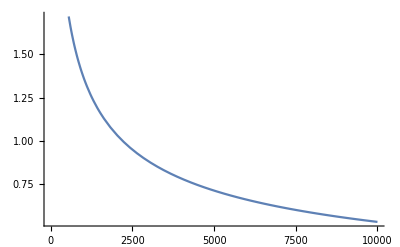

```mathematica
Plot[Sqrt[8/n*Log[4*m2/0.05]],{n,0,10000}]
```

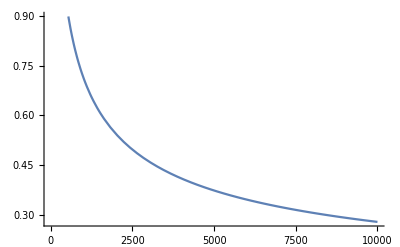

```mathematica
Plot[Sqrt[2*Log[2*n*m1]/n]+Sqrt[2/n*Log[1/0.05]]+1/n,{n,0,10000}]
```

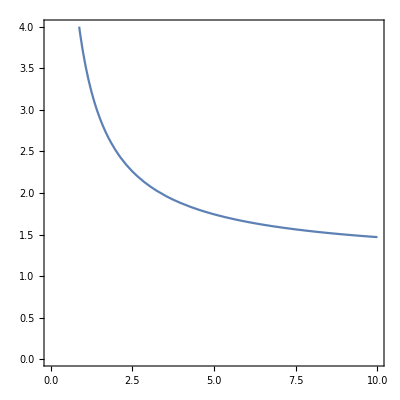

```mathematica
ContourPlot[y==Sqrt[1/n*(2*y+Log[6*m2/0.05])],{n,0,10},{y,0,4}]
```

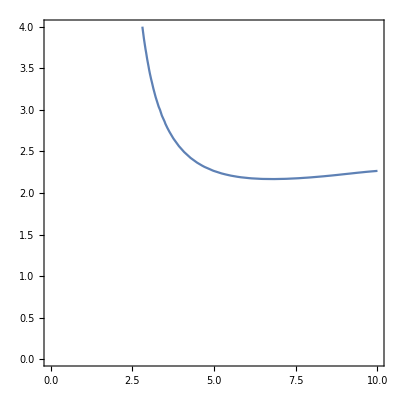

```mathematica
ContourPlot[y==Sqrt[1/2/n*(4*y*(1+y)+Log[4*m3/0.05])],{n,0,10},{y,0,4}]
```